```mathematica
Clear["Global`*"]
```

```mathematica
(* Импорт исходных данных *)
data = Import["/Users/dashavecherinka/Desktop/ВКР код/data.xlsx"];
lowerBound = data⟦1⟧;
upperBound = data⟦2⟧;
d =data⟦3⟧;
t0 = data⟦4⟧;
g = data⟦5⟧;
e00 = 0.01;
```

```mathematica
(*  Функции *)
ttf [variablesVectorC_, variablesVectorX_, g_]:= Module[
{variablesVectorC0 =variablesVectorC,
variablesVectorX0 = variablesVectorX,
g0 = g},
value = 0;
For[counter1 = 1, counter1 <= Length@g0, counter1++,
value = value + (g0⟦counter1,3⟧ + 0.15 * ((variablesVectorX0 ⟦g0⟦counter1,1⟧,g0⟦counter1,2⟧⟧/variablesVectorC0 ⟦g0⟦counter1,1⟧,g0⟦counter1,2⟧⟧)^4))
];
value 
]

icf [variablesVectorC_, lowerBound_, d_,g_]:= Module[
{variablesVectorC0 =variablesVectorC,
lowerBound0 = lowerBound,
d0 = d,
g0 = g}, 
value = 0;
For[counter1 = 1, counter1 <= Length@g0, counter1++,
value = value + (0.0000001* ((variablesVectorC0⟦g0⟦counter1,1⟧,g0⟦counter1,2⟧⟧ - lowerBound0⟦g0⟦counter1,1⟧,g0⟦counter1,2⟧⟧)^2))
];
value 
]

(* ЛеБланк *)
getFlowVector1[ G1_,n1_,D1_] := Module [
{G0 = G1 ,
n0 =n1,
D0 =D1
},
X1 = Table[0,n0,n0];
For[iCounter = 1., iCounter ≤ n0, iCounter ++,
For[jCounter = 1., jCounter ≤ n0, jCounter ++,
If[iCounter ≠ jCounter,
{p = FindShortestPath[G0,iCounter, jCounter],
For[lCounter = 1, lCounter ≤( Length@p-1),lCounter++,
X1⟦p⟦lCounter⟧,p⟦lCounter+1⟧⟧ = X1⟦p⟦lCounter⟧,p⟦lCounter+1⟧⟧ + D0⟦iCounter,jCounter⟧
]
}
]
]
]
]

getFlowVector2[ G1_,n1_,D1_] := Module [
{G0 = G1 ,
n0 =n1,
D0 =D1
},
Y1 = Table[0,n0,n0];
For[iCounter = 1., iCounter ≤ n0, iCounter ++,
For[jCounter = 1., jCounter ≤ n0, jCounter ++,
If[iCounter ≠ jCounter,
{p = FindShortestPath[G0,iCounter, jCounter],
For[lCounter = 1, lCounter ≤( Length@p-1),lCounter++,
Y1⟦p⟦lCounter⟧,p⟦lCounter+1⟧⟧ = Y1⟦p⟦lCounter⟧,p⟦lCounter+1⟧⟧ + D0⟦iCounter,jCounter⟧
]
}
]
]
]
]
leBlanc[T01_,D1_,C1_,e1_, g1_] := Module[
{T0 = T01 ,
D0 =D1,
C0 =C1,
e0 = e1,
g0 = g1
},
n = D0//Length;
stop = False;
edges = UndirectedEdge[#⟦1⟧,#⟦2⟧]&/@g0;
G = Graph[edges, EdgeWeight->(Transpose@g0)⟦3⟧];
X1 = {};
getFlowVector1[G,n,D0];
iterationNum = 1;

While [stop ≠ True,

T1=Table[0,{i,n},{j,n}];

For[iCounter = 1, iCounter ≤ n, iCounter++,
For[jCounter = 1, jCounter ≤ n, jCounter++,
If[C0⟦iCounter,jCounter⟧≠ 0,
T1⟦iCounter, jCounter⟧ = T0⟦iCounter,jCounter⟧*(1+0.15*(X1⟦iCounter,jCounter⟧/C0⟦iCounter,jCounter⟧)^4)
]
]
];

For[iCounter = 1, iCounter ≤Length@g0, iCounter++,
g0⟦iCounter, 3⟧ = T1⟦g0⟦iCounter, 1⟧,g0⟦iCounter, 2⟧⟧
];
edges1 = UndirectedEdge[#⟦1⟧,#⟦2⟧]&/@g0;
G1 = Graph[edges1, EdgeWeight->(Transpose@g0)⟦3⟧];

 getFlowVector2[ G1,n,D0];

Ccalc =Table[0,{counter,n},{counter2,n}];

For[iCounter = 1, iCounter ≤ n, iCounter++,
For[jCounter = 1, jCounter ≤ n, jCounter++,
If[C0⟦iCounter,jCounter⟧≠ 0,
Ccalc⟦iCounter, jCounter⟧ = 1/(C0⟦iCounter, jCounter⟧^4)
]
]
];

h=0.001;
l= Table[counter,{counter,0,1,h}];
For[counter = 1, counter ≤( Length@l-1),counter++,
dfi =Total@( Total[T0*(Y1-X1)+0.15*T0*Ccalc*((X1+l⟦counter⟧*(Y1-X1))^4)*(Y1-X1)]);
dfiplus1 =Total@( Total[T0*(Y1-X1)+0.15*T0*Ccalc*((X1+l⟦counter+1⟧*(Y1-X1))^4)*(Y1-X1)]);
If[RealSign[dfi]≠ RealSign[dfiplus1],
{
lambda=(h*counter +h/2),
counter = (Length@l+1)
},
lambda=0.5;
]
];

X2 = X1 + lambda*(Y1-X1);

difVal =  Table[0,n,n];
For[iCounter = 1, iCounter ≤ n, iCounter++,
For[jCounter = 1, jCounter ≤ n, jCounter++,
If[X1⟦iCounter,jCounter⟧≠ 0,
difVal ⟦iCounter, jCounter⟧ = (X2⟦iCounter, jCounter⟧ -X1⟦iCounter, jCounter⟧ )/X1⟦iCounter, jCounter⟧ 
]
]
];

If[Max[Abs@difVal]<e0,
stop=True,
{
stop=False,
X1=X2,
iterationNum++

}
];
];
X1
]

(* Функция весового коэффициента *)
wLin[ tmax_,t_,wmin_,wmax_] := Module [
{tmax0= tmax ,
t0 =t,
wmin0 =wmin,
wmax0 = wmax
},
w=(tmax0-t0)/tmax0*(wmax0-wmin0)+wmin0;
w
]
```

```mathematica
(* Исходные переменные *)
iterrationCounter = 1;
iterrationsAmount = 100;
particlesAmount = 20;

w= 0.5;
wmin = 1;
wmax = 0.3;
c1 = 0.2;
c2 = 0.2;

particlesPosition = {};
particlesValue = {};
bestParticlesPosition = {};
bestParticlesValue = {};
particlesVelocity =  Table[0, particlesAmount, Length@lowerBound,Length@lowerBound];

bestValue = {};
bestPosition  = {};

variablesVectorX  ={};

bestValueList = {};
bestPositionList ={};
bestParticlesValueList ={};
variablesVectorXList = {};
ttfMinList = {};
icfMinList = {};
```

```mathematica
(* Инициализация переменных верхнего уровня *)
For[k = 1, k<= particlesAmount, k++,
variablesVectorC = Table[0, Length@lowerBound,Length@lowerBound];
For[i = 1, i<= Length@lowerBound, i++,
For[j = 1, j <= Length@lowerBound, j++,
variablesVectorC⟦i,j⟧ = RandomReal[{lowerBound⟦i, j⟧,upperBound⟦i, j⟧}]
]
];
particlesPosition = Append[particlesPosition,variablesVectorC ]
]
(* Инициализация переменных нижнего уровня *)
For[k = 1, k<= particlesAmount, k++,
leBlanc[t0,d,particlesPosition⟦k⟧,e00, g];
variablesVectorX = Append[variablesVectorX ,X1];
Print@k
]
```

```mathematica
(* Первый пересчет *)
bestValueList = {};
bestPositionList ={};
bestParticlesValueList ={};
variablesVectorXList = {};

particlesValue = {};
For[i = 1, i<= particlesAmount, i++,
particlesValue = Append[particlesValue,  ttf[particlesPosition⟦i⟧, variablesVectorX⟦i⟧, g]+icf[particlesPosition⟦i⟧, lowerBound, d,g]
];
]
bestParticlesValue = particlesValue;
bestParticlesPosition = particlesPosition; 
bestValue = Min@bestParticlesValue;
bestPosition = bestParticlesPosition⟦Position[ bestParticlesValue,Min@bestParticlesValue]⟦1,1⟧⟧;

bestValueList = Append[bestValueList,bestValue ];
bestPositionList= Append[bestPositionList,bestPosition ];
bestParticlesValueList  = Append[bestParticlesValueList ,bestParticlesValue ];
variablesVectorXList = Append[variablesVectorXList,variablesVectorX];
```

```mathematica
(* Оптимизация на верхнем уровне алгоритмом PSO *)
```

```mathematica
iterrationsAmount = 150;

While[ iterrationCounter <= iterrationsAmount,
(* Пересчет скорости и позиции частиц *)
For[k = 1, k<= particlesAmount, k++,
For[i= 1, i<=Length@lowerBound, i++,
For[j= 1, j<=Length@lowerBound, j++,
particlesVelocity⟦k, i, j⟧ = wLin[ iterrationsAmount,iterrationCounter,wmax/wmax,wmin/wmax]  * particlesVelocity⟦k, i, j⟧ + RandomReal[]*c1 * (bestParticlesPosition⟦k,i,j⟧ - particlesPosition⟦k, i, j⟧) + 
 RandomReal[]*c2 * (bestPosition⟦i,j⟧ - particlesPosition⟦k, i, j⟧ );
particlesPosition⟦k, i, j⟧ = particlesPosition⟦k, i, j⟧ +particlesVelocity⟦k, i, j⟧;
If[particlesPosition⟦k, i, j⟧ < lowerBound ⟦i,j⟧,
particlesPosition⟦k, i, j⟧ = lowerBound ⟦i,j⟧
,
If[particlesPosition⟦k, i, j⟧ > upperBound⟦i,j⟧,
particlesPosition⟦k, i, j⟧ = upperBound⟦i,j⟧
]
]
]
]
];

(* Пересчет переменных на нижнем уровне *)
variablesVectorX ={};
For[k = 1, k<= particlesAmount, k++,
leBlanc[t0,d,particlesPosition⟦k⟧,e00, g];
variablesVectorX = Append[variablesVectorX ,X1];
Print@k
];

(* Пересчет значения целевой функции *)
particlesValue = {};
For[i = 1, i<= particlesAmount, i++,
particlesValue = Append[particlesValue,  ttf[particlesPosition⟦i⟧, variablesVectorX⟦i⟧, g]+icf[particlesPosition⟦i⟧, lowerBound, d,g]
]
];

(* Пересчет лучших значений *)
For[k =1, k<= particlesAmount, k++,
If[bestParticlesValue⟦k⟧ > particlesValue⟦k⟧,
{
bestParticlesValue⟦k⟧ = particlesValue⟦k⟧;
bestParticlesPosition⟦k⟧ = particlesPosition⟦k⟧
} 
];
If[bestValue > particlesValue⟦k⟧,
{
bestValue = particlesValue⟦k⟧,
bestPosition = particlesPosition⟦k⟧
}
]
];


bestValueList = Append[bestValueList,bestValue ];
bestPositionList= Append[bestPositionList,bestPosition ];
bestParticlesValueList  = Append[bestParticlesValueList ,bestParticlesValue ];
variablesVectorXList = Append[variablesVectorXList,variablesVectorX];

iterrationCounter++;
Print@iterrationCounter;
Print@bestValue;
Print@bestPosition;
Print@bestParticlesValue;
Print@(bestValue//Total//Total)
]
```

```mathematica
(* Изменение лучших значений *)
bestValueList ⟦#-1⟧-bestValueList ⟦#⟧&/@Range[2,bestValueList//Length]
```

{0.662667,2.66051,0.584186,0.572059,1.78668,0.,0.611478,0.880443,0.,0.30676,0.113565,0.,0.118008,0.,0.,0.,0.,0.,0.,0.00202829,0.237519,0.506299,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0179802,0.,0.,0.,0.,0.,1.66784×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.437565,0.,0.,0.,0.,0.,0.00664151,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000890358,0.0033456,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000520573,0.,0.,0.,0.,0.0000386826,0.000032401,0.0000271865,0.0000229472,0.0000194826,0.0000166364,0.,0.,0.,0.}

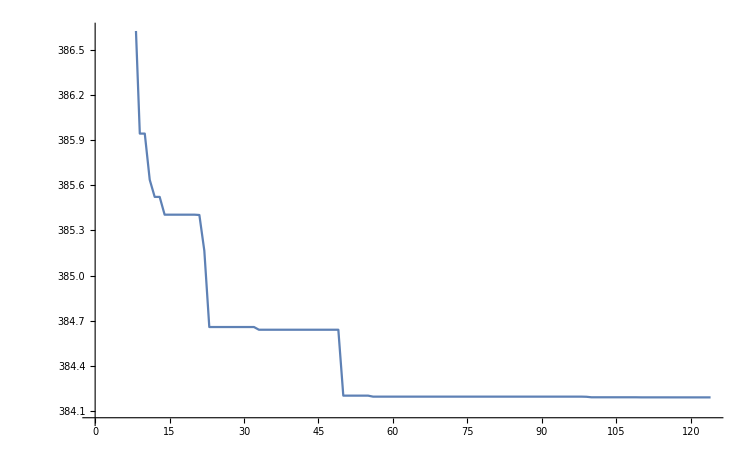

```mathematica
ListLinePlot[bestValueList]
```

```mathematica
(* Визуализация матрицы спроса на перемещение *)
MatrixPlot[d,Mesh->True,PlotTheme->"Detailed"]
```

-Graphics-

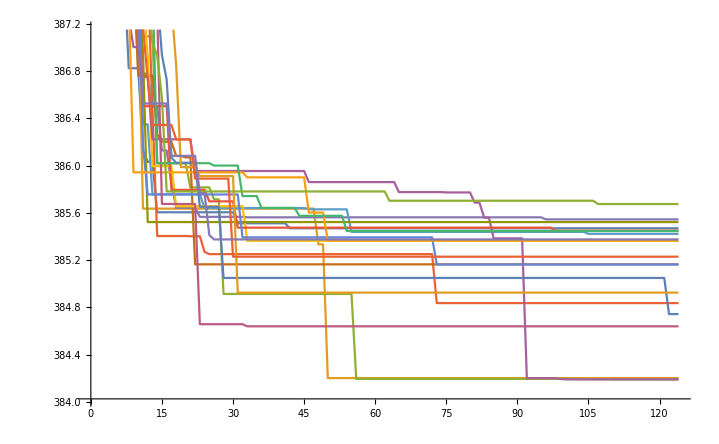

```mathematica
(* Изменение лучшего положения каждой из частиц *)
ListLinePlot[Table[(Transpose@bestParticlesValueList)⟦i⟧,{i, Length@bestParticlesValue}]]
```

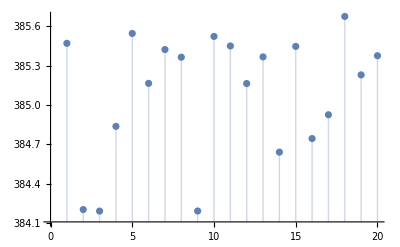

```mathematica
ListPlot[bestParticlesValue,Filling->Axis]
```

```mathematica
bestPosition//MatrixForm
```

(0. | 26405.2 | 24280.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
27411.3 | 0. | 0. | 0. | 0. | 6144.41 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
23897.1 | 0. | 0. | 17959. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 24728.7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 19002.7 | 0. | 19827.5 | 0. | 0. | 0. | 0. | 0. | 5893.06 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 18006. | 0. | 5545.22 | 0. | 0. | 10106.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 7533.5 | 0. | 0. | 7442.06 | 0. | 0. | 5298.57 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 9584.92 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 23910.2 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 5341.86 | 9078.56 | 0. | 5193.13 | 0. | 0. | 0. | 0. | 0. | 0. | 5177.24 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 11979.6 | 0. | 0. | 6864.96 | 0. | 15573.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 14400.3 | 0. | 11154.2 | 0. | 0. | 0. | 14544.1 | 6122.72 | 6465.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 6166.74 | 0. | 0. | 0. | 0. | 0. | 13633.8 | 0. | 6872.69 | 0. | 7844.19 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 24884.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6615.28 | 0. | 28022.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 28493.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7378.71
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6021.13 | 0. | 0. | 0. | 6730.38 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7526.45 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15453.4 | 0. | 0. | 0. | 5386.44 | 0. | 0. | 0. | 0. | 15864.7 | 0. | 0. | 10393.3 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 6347.53 | 0. | 6781.51 | 0. | 0. | 0. | 0. | 0. | 0. | 6172.38 | 22247.1 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5246.03 | 0. | 0. | 0. | 0. | 0. | 6279.57 | 0. | 0. | 6575.85 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 24730.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20872.8 | 0. | 0. | 0. | 24740.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15945.2 | 0. | 7385.98 | 0. | 0. | 7188.8 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 23737.5 | 7511.54 | 0. | 5499.99 | 5708.39 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5524.22 | 0. | 6765.31 | 0. | 5989.88
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9905.93 | 0. | 0. | 0. | 0. | 5121.42 | 7380.23 | 0. | 7427.51 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6347.71 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6255.52 | 0. | 6462.74
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5173.65 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5855.28 | 0. | 6196.04 | 0.)

```mathematica
MatrixPlot[variablesVectorX ⟦3⟧,PlotLegends->Automatic,PlotTheme->"Detailed",Mesh->All]
```

-Graphics-

{1.->2.,1.->3.,2.->6.,3.->4.,3.->12.,4.->5.,4.->11.,5.->6.,5.->9.,6.->8.,7.->8.,7.->18.,8.->9.,8.->16.,9.->10.,10.->11.,10.->15.,10.->16.,10.->17.,11.->12.,11.->14.,12.->13.,13.->24.,14.->15.,14.->23.,15.->19.,15.->22.,16.->17.,16.->18.,17.->19.,18.->20.,19.->20.,20.->21.,20.->22.,21.->22.,21.->24.,22.->23.,23.->24.,2.->1.,3.->1.,6.->2.,4.->3.,12.->3.,5.->4.,11.->4.,6.->5.,9.->5.,8.->6.,8.->7.,18.->7.,9.->8.,16.->8.,10.->9.,11.->10.,15.->10.,16.->10.,17.->10.,12.->11.,14.->11.,13.->12.,24.->13.,15.->14.,23.->14.,19.->15.,22.->15.,17.->16.,18.->16.,19.->17.,20.->18.,20.->19.,21.->20.,22.->20.,22.->21.,24.->21.,23.->22.,24.->23.}

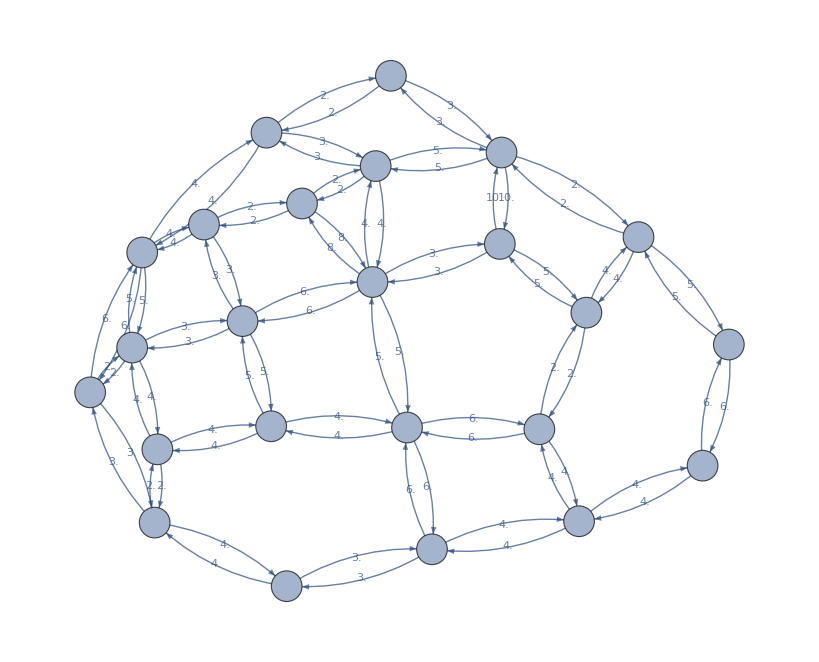

```mathematica
(* Визуализация исследуемого графа *)
edges = DirectedEdge[#⟦1⟧,#⟦2⟧]&/@g
G = Graph[edges, EdgeWeight->(Transpose@g)⟦3⟧,VertexSize->0.5,VertexLabels->Placed[Automatic,Center],EdgeLabels->Placed["EdgeWeight",Center]]
```